```mathematica
DataE = Import["/Users/sperkins/git-repos/gw_analysis_tools/data/Pw_three.csv"];
```

```mathematica
DataS = Import["/Users/sperkins/git-repos/gw_analysis_tools/data/Pw_3.csv"];
```

```mathematica
Sinterp = Interpolation[DataS]
```

InterpolatingFunction[…]

```mathematica
Einterp = Interpolation[DataE]
```

InterpolatingFunction[…]

```mathematica
Sinterp[.1]
```

0.998786

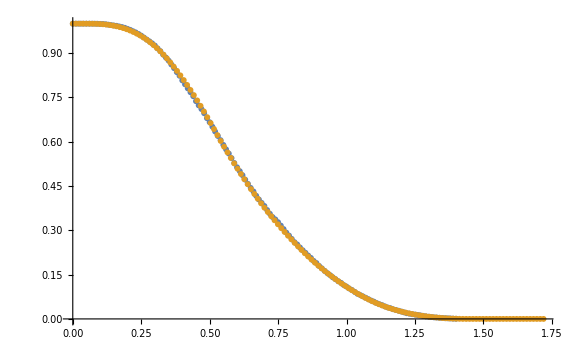

```mathematica
ListPlot[{DataE,DataS},ImageSize->Large]
```

```mathematica
Residual = Table[ {x,(Einterp[x]- Sinterp[x])/Einterp[x]},{i,1,Length[DataE]}];
```

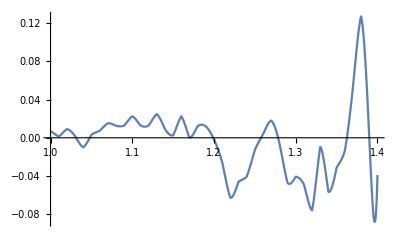

```mathematica
Plot[2(Einterp[x]- Sinterp[x])/(Einterp[x]+Sinterp[x]),{x,1,1.4},PlotRange->Full]
```

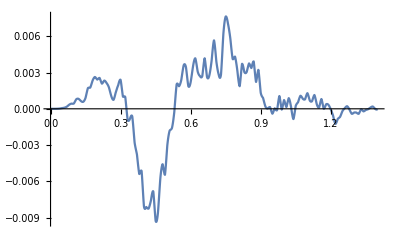

```mathematica
Plot[(Einterp[x]- Sinterp[x]),{x,0,1.4},PlotRange->Full]
```

```mathematica
DataE = Import["/Users/sperkins/git-repos/gw_analysis_tools/data/Pw_three.csv"];
```

```mathematica
DataS = Import["/Users/sperkins/git-repos/gw_analysis_tools/testing/data/P_triple.csv"];
```

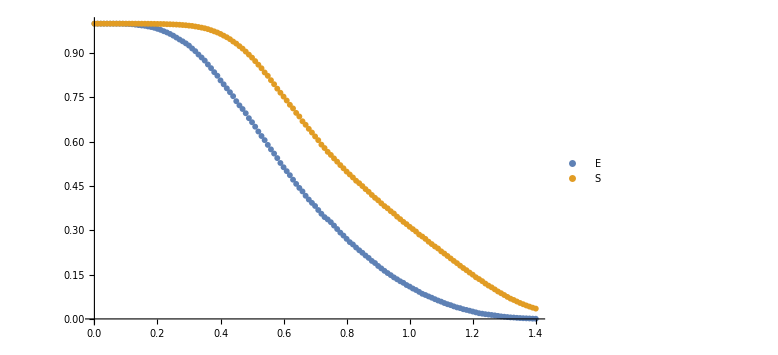

```mathematica
ListPlot[{DataE,DataS},ImageSize->Large,PlotLegends-> {"E","S"}]
```

```mathematica
Residual = Table[ {DataE[[i]][[1]],(DataE[[i]] [[2]]- DataS[[i]][[2]])/DataE[[i]][[2]]},{i,1,Length[DataE]}];
```

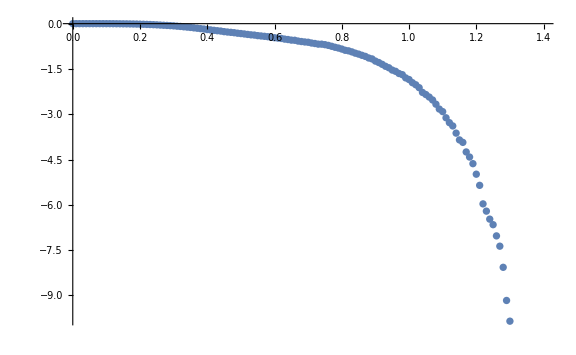

```mathematica
ListPlot[Residual,ImageSize->Large]
```

```mathematica
√((8.42989697626*^05)^2+(4.37857696241*^06)^2+(4.54637409900*^06)^2)
```

6.36805×10^6

```mathematica
√((-3777336.024)^2+(3484898.411)^2+(3765313.697)^2)
```

6.37106×10^6

```mathematica
√((1450526.82294155)^2+(6011058.39047265)^2+(1558018.27884102)^2)
```

6.37685×10^6